```mathematica
clearall
uval=NDSolveValue[{D[u[x,t],t,t]==D[u[x,t],x,x]- 10*x*D[u[x,t],x],u[0,t]==u[1,t]==0,u[x,0] == Sin[3Pi*x]},u,{x,0,1},{t,0,5}]
Animate[Plot[uval[x,t],{x, 0 ,1},PlotRange-> {{0,1},{-10,10}}],{t,0,5}]
```

clearall

InterpolatingFunction[…]

```mathematica
clearall
uval=NDSolveValue[{D[u[x,y,t],t,t]==D[u[x,y,t],x,x]- 10*x*D[u[x,y,t],x] + D[u[x,y,t],y,y],u[0,y,t]==u[1,y,t]==0,u[x,y,0] == Sin[Pi*x]},u,{x,0,1},{y,0,1},{t,0,5}]
Animate[Plot3D[uval[x,y,t],{x, 0 ,1},{y,0,1},PlotRange-> {{0,1},{0,1},{-10,10}}],{t,0,5}]
```

clearall

InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 5.}}, <>]

```mathematica
clearall
uval=NDSolveValue[{D[u[x,y,t],t,t]==D[u[x,y,t],x,x]- 10*x*D[u[x,y,t],x] + D[u[x,y,t],y,y],u[0,y,t]==u[1,y,t]==0,u[x,y,0] == Sin[Pi*x], If[y>3x,u[x,y,t] = 0],  If[y>-3x,u[x,y,t] == 0], u},u,{x,0,1},{y,0,1},{t,0,5}]
Animate[Plot3D[uval[x,y,t],{x, 0 ,1},{y,0,1},PlotRange-> {{0,1},{0,1},{-10,10}}],{t,0,5}]
```

clearall

NDSolveValue::deqn: Equation or list of equations expected instead of True in the first argument {True,u[0,y,t]==u[1,y,t]==0,u[x,y,0]==Sin[3 π x],u}.

NDSolveValue[{True,u[0,y,t]==u[1,y,t]==0,u[x,y,0]==Sin[3 π x],u},u,{x,0,1},{y,0,1},{t,0,5}]

```mathematica
clearall
f[x_,y_,t_] := 
uval=NDSolveValue[{D[u[x,y,t],t,t]==D[u[x,y,t],x,x]- 10*x*D[u[x,y,t],x] + D[u[x,y,t],y,y],u[0,y,t]==u[1,y,t]==0,u[x,y,0] == Sin[Pi*x],  f[x,y,t]},u,{x,0,1},{y,0,1},{t,0,5}]
Animate[Plot3D[uval[x,y,t],{x, 0 ,1},{y,0,1},PlotRange-> {{0,1},{0,1},{-10,10}}],{t,0,5}]
```

clearall

clearall

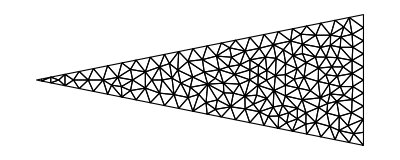

NDSolveValue::deqn: Equation or list of equations expected instead of False in the first argument {(u^(2,0,0)[t,x,y]==u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y])==0,DirichletCondition[u[t,x,y]==0,x==0||x==0.1],u[0,x,y]==Sin[π x],False}.

NDSolveValue[{(u^(2,0,0)[t,x,y]==u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y])==0,DirichletCondition[u[t,x,y]==0,x==0||x==0.1],u[0,x,y]==Sin[π x],False},u,{x,y}∈ElementMesh[{{0.,1.},{-0.2,0.2}},{TriangleElement[<318>]}],{t,0,0.1}]

NDSolveValue::deqn: Equation or list of equations expected instead of False in the first argument {(u^(2,0,0)[t,x,y]==u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y])==0,DirichletCondition[u[t,x,y]==0,x==0||x==0.1],u[0,x,y]==Sin[π x],False}.

NDSolveValue[{(u^(2,0,0)[t,x,y]==u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y])==0,DirichletCondition[u[t,x,y]==0,x==0||x==0.1],u[0,x,y]==Sin[π x],False},u,{x,y}∈ElementMesh[{{0.,1.},{-0.2,0.2}},{TriangleElement[<318>]}],{t,0,0.1}]

```mathematica
clearall
Needs["NDSolve`FEM`"]
omega = ImplicitRegion[0≤x≤1&&.2x≤y≤-.2x, {x,y}];
mesh = ToElementMesh[omega];
%["Wireframe"]
op=D[u[t,x,y],t,t]==D[u[t,x,y],x,x]+ D[u[t,x,y],y,y];
gamma1=DirichletCondition[u[t,x,y]==0,x==0||x==.1];
ic = u[0,x,y] == Sin[Pi*x];
dic=D[u[0,x,y],t]==1;
NDSolveValue[{op==0,gamma1,ic,dic},u,Element[{x,y},mesh],{t,0,.1}]
uval = NDSolveValue[{op==0,gamma1,ic,dic},u,Element[{x,y},mesh],{t,0,.1}]
Animate[Plot3D[uval[x,y,t],{x, 0 ,1},{y,0,1}],{t,0,1}]
```

```mathematica
- 10*x*D[u[x,y,t],x] + D[u[x,y,t],y,y]
```

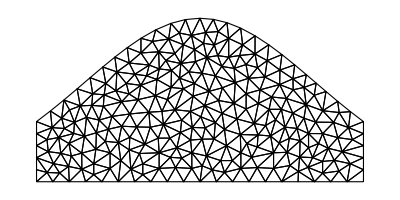

NDSolveValue::fememrc: The ranges {{0.,3.},«1»} cannot be combined to a region. Please specify a combined region.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {u^(2,0,0)[t,x,y]==u^(0,0,2)[t,x,y]-10 x u^(0,1,0)[t,x,y]+u^(0,2,0)[t,x,y],DirichletCondition[u[t,x,y]==0,x==1||x==-1],DirichletCondition[u[t,x,y]==1,y==0],u[0,x,y]==1}.

```mathematica
Needs["NDSolve`FEM`"];
Clear[u];
omega=ImplicitRegion[-1≤x≤1&&0≤y≤Exp[-x^2],{x,y}];
mesh=ToElementMesh[omega];
%["Wireframe"]
op = 
gamma1=DirichletCondition[u[t,x,y]==0,x==1||x==-1];
gamma2=DirichletCondition[u[t,x,y]==1,y==0];
u=NDSolveValue[{D[u[t,x,y],t,t]==D[u[t,x,y],x,x]- 10*x*D[u[t,x,y],x]+ D[u[t,x,y],y,y],gamma1,gamma2,u[0,x,y]==1},u,Element[{x,y},mesh],{t,0,3}];
```

```mathematica
ufunWave=NDSolveValue[{op==0,ic,dic,Subscript[Γ,D]},u,{t,0,2 π},]
```

```mathematica
clearall
heatsol=NDSolveValue[{Derivative[0,2,0][u][t,x,y]+Derivative[0,0,2][u][t,x,y]-Derivative[2 (*changed from 1*),0,0][u][t,x,y]==0,DirichletCondition[u[t,x,y]==Sin[2 Pi t],True],u[0,x,y]==0,(Derivative[1,0,0][u][tt,x,y]/.tt->0)==0},u,{t,0,1},{x,y}∈mesh]

Plot3D[heatsol[t,x,y],{x,y}∈mesh,PlotRange->{-3,3}]
```

clearall

InterpolatingFunction[{{0., 1.}, {0., 1.}, {-0.2, 0.2}}, <>]

-Graphics3D-

```mathematica
clearall
Ω=ImplicitRegion[0≤x≤1&&.2x-.2≤y≤-.2x + .2, {x,y}];
uifWave = NDSolveValue[{D[u[t,x,y], t,t]- D[u[t,x,y],x,x]-D[u[t,x,y],y,y]+100*x*D[u[t,x,y],x] == 0, 
     u[0, x, y] == Sin[10*Pi*x], 
	Derivative[1,0,0][u][0, x, y] == 0, 
DirichletCondition[u[t, x, y] == 0, True]}, 
    u, {t, 0, 2 π}, {x, y} ∈ Ω] // Quiet;
(*framesWEQ=Table[Plot3D[uifWave[t,x,y],{x,y}∈uifWave["ElementMesh"],PlotRange->{-1,1},Boxed->False,Axes->False,Mesh->None],{t,0,2 π,2 π/50}];
Manipulate[framesWEQ[[i]],{{i,16,"time"},1,Length[framesWEQ],1},SaveDefinitions->True]*)

Animate[Plot3D[uifWave[t,x,y],{x,y}∈uifWave["ElementMesh"],PlotRange->{-100,100},Boxed->False,Axes->False,Mesh->None],{t,0,2*Pi,Pi/10}]
```

clearall

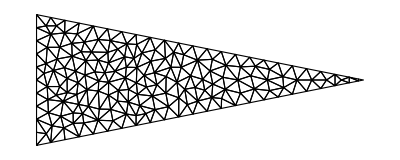

```mathematica
Needs["NDSolve`FEM`"]
omega = ImplicitRegion[0≤x≤1&&.2x-.2≤y≤-.2x + .2, {x,y}];
mesh = ToElementMesh[omega];
%["Wireframe"]
```